```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/"]
```

/home/waleed/Documents/Wolfram_Mathematica/TransportFunction

```mathematica
Get["Spectra/ElectronSpectrum.m"]
Get["Spectra/Glueck93ProtonSpectrum.m"]
```

### settings

```mathematica
SeedRandom[1000]
```

```mathematica
SpectrumDir="~/FerencSource+Spectra/Mma_Spectra_1e8_2e3_Glueck93_thMax45";
```

```mathematica
TotalNumber=1*10^7;
PackageSize=2*10^3;
DataSets=TotalNumber/PackageSize
```

5000

```mathematica
ThetaMax=Pi/4;
```

```mathematica
SetDirectory["~/FourTb/MC_TrajProton/"]
```

/home/waleed/FourTb/MC_TrajProton

```mathematica
CloseKernels[]
```

{KernelObject[1,local,<defunct>],KernelObject[2,local,<defunct>],KernelObject[3,local,<defunct>],KernelObject[4,local,<defunct>]}

```mathematica
LaunchKernels[]
```

{KernelObject[1,local],KernelObject[2,local],KernelObject[3,local],KernelObject[4,local],KernelObject[5,local],KernelObject[6,local]}

## Energy-Spectra definition

```mathematica
ElectronSpectrumPDF=ProbabilityDistribution[weNormed[λ0,κ0,0,Ee],{Ee,me,E0}]
```

ProbabilityDistribution[1.67491×10^-29 (1+0.170558 (-5.98404 (0.00275144+555.831/x-4.25729×10^-9 x)+1.62104 (-0.00275144-555.831/x+1.06432×10^-8 x)+2.12864×10^-9 x)) (1.29258×10^6-x)^2 x √(-2.6112×10^11+x^2) (Piecewise[{{231.822, x<510999.}, {(2 π)/(137 √(1-(2.6112×10^11)/x^2) (1-ⅇ^(-(2 π)/(137 √(1-(2.6112×10^11)/x^2))))), True}}]) (1+InterpolatingFunction[…][x]),{x,510999.,1.29258×10^6}]

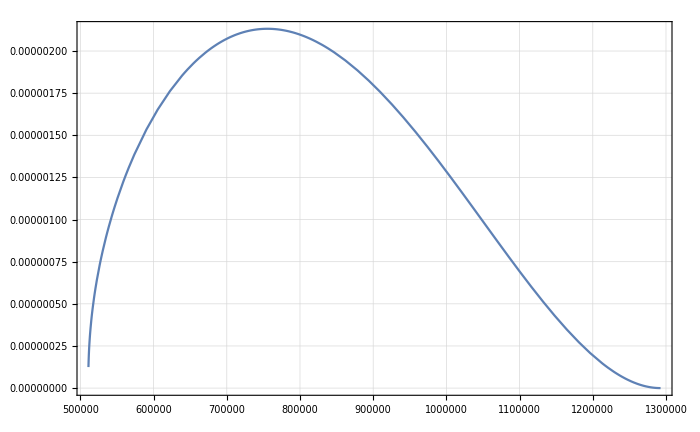

```mathematica
Plot[PDF[ElectronSpectrumPDF,Ee],{Ee,me,E0}]
```

```mathematica
NIntegrate[PDF[ElectronSpectrumPDF,Ee],{Ee,me,E0}]
```

1.

```mathematica
ProtonSpectrumPDF=ProbabilityDistribution[wpNormedGlueck93[T,λ0,κ0],{T,0.,tpMax}]
```

ProbabilityDistribution[1.4278×10^-30 omega0Calpha[9.38272×10^8+x,-1.2732,1.85],{x,0.,751.192}]

InterpolatingFunction::dmval: Input value {0.0000204286} lies outside the range of data in the interpolating function. Extrapolation will be used.

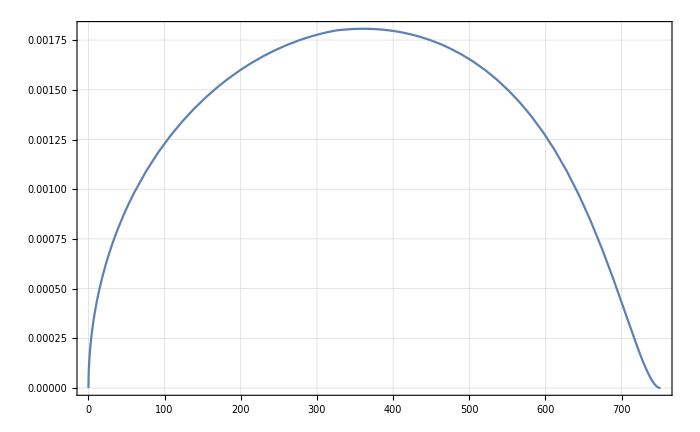

```mathematica
Plot[PDF[ProtonSpectrumPDF,T],{T,0,tpMax}]
```

```mathematica
NIntegrate[PDF[ProtonSpectrumPDF,T],{T,0,tpMax}]
```

1.

## ThetaDist

```mathematica
ThetaMax
```

π/4

```mathematica
ThetaMaxDegree=180.
```

180.

```mathematica
360/180*Pi
```

2 π

```mathematica
ThetaNorm=Integrate[Sin[th/180*Pi],{th,0,ThetaMaxDegree}]
```

114.592

```mathematica
ThetaPDF=ProbabilityDistribution[Sin[th/180.*Pi],{th,0,ThetaMaxDegree},Method->"Normalize"]
```

ProbabilityDistribution[0.00872665 Sin[0.0174533 x],{x,0,180.}]

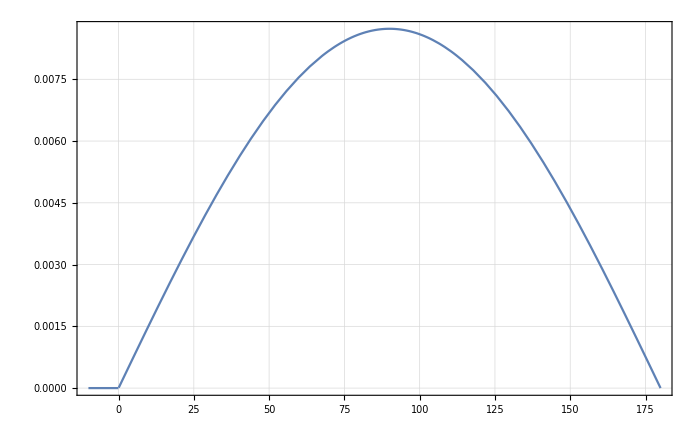

```mathematica
Plot[PDF[ThetaPDF,x],{x,-10,180}]
```

```mathematica
|
```

```mathematica
RandomVariate[ThetaPDF,10]
```

{27.9238,16.4453,22.1534,22.2234,21.6551,25.5216,19.9458,34.5892,9.93106,39.4868}

```mathematica
testdata=RandomVariate[ThetaPDF,10^3];
```

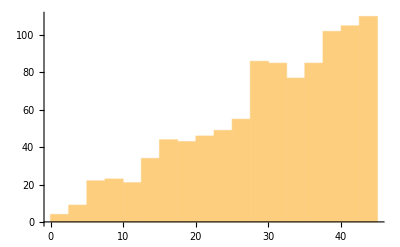

```mathematica
Histogram[testdata,{0,45,2.5}]
```

## Phi Uniform

```mathematica
PhiPDF=UniformDistribution[{0,360.}]
```

UniformDistribution[{0,360.}]

## create data

## electron energy also in eV

```mathematica
t0=AbsoluteTime[];
EeList=ParallelTable[RandomVariate[ElectronSpectrumPDF,PackageSize]-me,{DataSets}];
t1=AbsoluteTime[];
t1-t0
```

$Aborted

612.640714

```mathematica
EeList[[1,1;;10]]
```

{357829.,212773.,500251.,492669.,630753.,320610.,287717.,443733.,616803.,91494.6}

### proton Ekin

```mathematica
CloseKernels[]
LaunchKernels[]
```

{KernelObject[1,193.170.93.93,<defunct>],KernelObject[2,193.170.93.93,<defunct>],KernelObject[3,193.170.93.93,<defunct>],KernelObject[4,193.170.93.93,<defunct>],KernelObject[5,193.170.93.93,<defunct>],KernelObject[6,193.170.93.93,<defunct>],KernelObject[14,local,<defunct>],KernelObject[15,193.170.93.100,<defunct>],KernelObject[16,193.170.93.100,<defunct>],KernelObject[17,193.170.93.100,<defunct>],KernelObject[20,193.170.93.100,<defunct>],KernelObject[22,local,<defunct>],KernelObject[23,local,<defunct>],KernelObject[24,193.170.93.100,<defunct>]}

{KernelObject[25,193.170.93.93],KernelObject[26,193.170.93.93],KernelObject[27,193.170.93.93],KernelObject[28,193.170.93.93],KernelObject[29,193.170.93.93],KernelObject[30,193.170.93.93],KernelObject[31,193.170.93.100],KernelObject[32,193.170.93.100],KernelObject[33,193.170.93.100],KernelObject[34,193.170.93.100],KernelObject[35,193.170.93.100],KernelObject[36,local],KernelObject[37,local]}

```mathematica
t0=AbsoluteTime[];
TpList=ParallelTable[RandomVariate[ProtonSpectrumPDF,PackageSize],{DataSets}];
t1=AbsoluteTime[];
t1-t0
```

InterpolatingFunction::dmval: Input value {0.078643} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0573677} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0690658} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.92125} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0844647} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0573677} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0868999} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0817348} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0844647} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0312985} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0868999} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0817348} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0976886} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0754484} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0592362} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0592362} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0850566} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0865024} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0850566} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0811765} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.980534} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.901937} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0753881} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0326229} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0811765} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.05765} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.980534} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.957992} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0753881} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0326229} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.902518} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.05765} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0944159} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0852658} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.969133} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0812796} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.971095} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0852658} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0211794} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.923306} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0581029} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0199858} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0291855} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0690091} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.901111} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.923311} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0401914} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.974386} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0148238} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.962057} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.00738629} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0224886} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.955293} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0175974} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0227641} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0965977} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.908049} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.954995} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0811719} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0321892} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.086774} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0491461} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.987418} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.953106} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.959342} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.946728} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.960104} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.00130296} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0309112} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0715209} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.919785} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.947351} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.980886} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0902064} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0446039} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0226269} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.911891} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.959741} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.970657} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0164511} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.936209} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.02297} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0368953} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.923585} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0778034} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.940495} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.915406} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.911096} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0118833} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.951332} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0657879} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.905423} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0227248} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0928033} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.905706} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0933209} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0942115} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.952549} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.924477} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.091332} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.953967} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0903446} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0384342} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0566481} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0868241} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.910629} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.943131} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.939751} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0373493} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.915105} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.931053} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.967709} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0131564} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.940886} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.948755} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.9478} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.927383} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0863274} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0364768} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0151156} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.099105} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.981364} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0793221} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.958353} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.926424} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0477487} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0586123} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0740315} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0861224} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.912292} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.901228} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.996824} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0566992} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.929054} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0408858} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0367319} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.913622} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0625216} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.032045} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.926948} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.956813} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.976378} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0487231} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.904825} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.946231} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0383572} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0379111} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.04523} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.015914} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.040828} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.00312151} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0471015} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0732039} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0596423} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.934048} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.92426} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.932514} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0080948} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.00987409} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.078818} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0350015} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.997747} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.065303} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0503778} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0203341} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0609981} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0488067} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0444868} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0870964} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0963309} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0696559} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0394743} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.048352} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.910209} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0248093} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0254398} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.914631} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.06913} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.958972} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.914004} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0885071} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0963418} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.986694} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0912891} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0971875} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0732093} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0215622} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.962401} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.944848} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0854272} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0861402} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.957225} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.900649} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.943869} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0933913} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0547809} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0557604} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0376587} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0561719} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0100965} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.963045} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0850336} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0217577} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0721763} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0911914} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.946815} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0347007} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0850299} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.93005} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0884421} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.930884} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0117223} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0417065} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.974139} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0325431} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.947946} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0351308} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.911549} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.087334} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0466811} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0533482} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0538551} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.905929} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.979766} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.99317} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.928567} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.00927222} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0594263} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0349091} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0538175} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0376376} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.963565} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0412636} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0962948} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.906653} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.981516} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.936172} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0752946} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.00767584} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.909147} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0570345} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0525896} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0676872} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0468435} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0928522} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0768166} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0718224} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0872135} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0666021} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0963545} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.956974} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.904224} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0115006} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.90864} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0964241} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.082895} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.98727} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0252444} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0233165} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0701455} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.91268} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0729775} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.922395} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.933779} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0895647} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.934485} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0682096} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0490405} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0993813} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.979973} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.985369} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0653683} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0780487} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.933717} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.00670301} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0783261} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0943152} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.905833} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.918949} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0925148} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.96287} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.900758} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.918515} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0831807} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.918308} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.946005} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.973227} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0425754} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.943763} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.915747} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0627479} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.99394} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.95522} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0962551} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0951044} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.939736} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0893283} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0832048} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0118898} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.91867} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0284283} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.913139} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0568237} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.927141} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.930407} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.959725} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.973434} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0538266} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.915062} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0885595} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.919017} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0707575} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.981885} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0985751} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.925467} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.926189} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.992304} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.965458} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0127504} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0867772} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0424315} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0694294} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0929959} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0985854} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0968435} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.924341} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0168004} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0434001} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0614897} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0972907} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.034356} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0647715} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0320039} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0329867} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0081219} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.934597} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.919368} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0492694} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.905887} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.956768} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.918399} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.972646} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0939354} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0675884} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0902875} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0836538} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0419071} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.951572} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0204425} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0751547} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.092944} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0334406} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.00797027} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0392038} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0722641} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.954198} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0951835} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0440403} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0914527} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0638138} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.983418} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0274487} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.908013} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0286188} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.930984} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.00729778} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0785041} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.946738} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0959196} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0615548} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0148913} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.942324} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.9188} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0370991} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.907488} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.962606} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0758707} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.081093} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.905626} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0587671} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0752751} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.043905} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0166058} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.975534} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.915723} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0335091} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0588917} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0740123} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.945985} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0582447} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0702245} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.940993} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.963633} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0954449} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0842697} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.918695} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.00486339} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0898428} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.031648} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.928617} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.00604285} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.933709} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0377804} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.915219} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.000975972} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.914643} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0430913} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0601109} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0959518} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.935973} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0886157} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0950144} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.934445} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.92406} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0479237} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.952527} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0612253} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0386335} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.000259698} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.917684} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.920922} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.961808} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0992764} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.953089} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0459494} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.02586} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.900387} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.94778} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0627067} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0786269} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0442968} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0757117} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0692102} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.937586} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0702794} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.079445} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0897365} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.902271} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.925323} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.912914} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0362551} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0682149} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0926765} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0173946} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.906897} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.093742} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.971841} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0345532} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0599981} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0990614} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0154872} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.98091} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0464209} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.03849} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.034004} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0649535} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.917043} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0115538} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

134207.91929

## Theta

```mathematica
ClearAll[ThetaList]
```

```mathematica
t0=AbsoluteTime[];
ThetaList=ParallelTable[RandomVariate[ThetaPDF,PackageSize],{DataSets}];
t1=AbsoluteTime[];
t1-t0
```

6.830409

```mathematica
ThetaList[[1,1;;10]]
```

{35.7078,36.2308,37.7103,28.2211,17.4618,24.5143,36.3809,30.7473,25.8904,44.2258}

```mathematica
ThetaList//Dimensions
```

{50000,2000}

### takes 1513s for 3 cores,

## Phi

```mathematica
t0=AbsoluteTime[];
PhiList=ParallelTable[RandomVariate[PhiPDF,PackageSize],{DataSets}];
t1=AbsoluteTime[];
t1-t0
```

10.37066

# data check

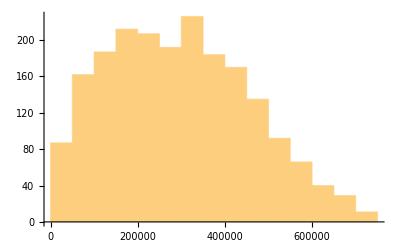

```mathematica
Histogram[EeList[[5]]]
```

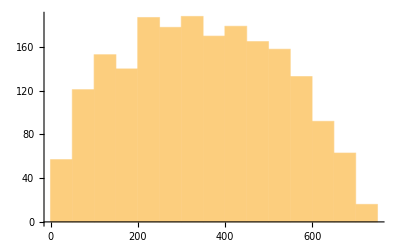

```mathematica
Histogram[TpList[[9]]]
```

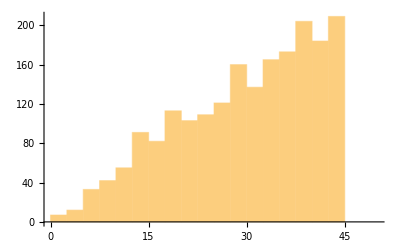

```mathematica
Histogram[ThetaList[[1]],{0,50,2.5}]
```

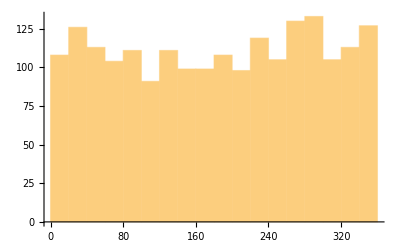

```mathematica
Histogram[PhiList[[1]]]
```

# export

```mathematica
PackageSize
```

2000

```mathematica
Which[PackageSize==10^4,PackageString="1e4_",PackageSize==2*10^3,PackageString="2e3_"]
```

2e3_

```mathematica
DataSets
```

50000

```mathematica
CloseKernels[]
LaunchKernels[2]
```

{KernelObject[25,193.170.93.93,<defunct>],KernelObject[26,193.170.93.93,<defunct>],KernelObject[27,193.170.93.93,<defunct>],KernelObject[28,193.170.93.93,<defunct>],KernelObject[29,193.170.93.93,<defunct>],KernelObject[30,193.170.93.93,<defunct>],KernelObject[31,193.170.93.100,<defunct>],KernelObject[32,193.170.93.100,<defunct>],KernelObject[33,193.170.93.100,<defunct>],KernelObject[34,193.170.93.100,<defunct>],KernelObject[35,193.170.93.100,<defunct>],KernelObject[36,local,<defunct>],KernelObject[37,local,<defunct>]}

{KernelObject[38,local],KernelObject[39,local]}

/home/waleed/FourTb/MC_TrajProton/SpectraElec

```mathematica
DataSets
```

5000

```mathematica
1-2000
```

```mathematica
2001-4000
```

```mathematica
2*1000
```

2000

```mathematica
k=0
```

0

```mathematica
4000*500
```

2000000

```mathematica
Table[j,{j,2},{i,10}]
```

{{1,1,1,1,1,1,1,1,1,1},{2,2,2,2,2,2,2,2,2,2}}

```mathematica
ThetaList2=Flatten[ThetaList,1];PhiList2=Flatten[PhiList,1];EeList2=Flatten[EeList,1];
```

```mathematica
k=0;ThetaList3=Table[k=k+1;ThetaList2[[k]],{i,2000},{j,500}];
k=0;PhiList3=Table[k=k+1;PhiList2[[k]],{i,2000},{j,500}];
k=0;EeList3=Table[k=k+1;EeList2[[k]],{i,2000},{j,500}];
```

```mathematica
ThetaList3[[1]]//Length
```

1000

```mathematica
ThetaList3//Length
```

1000

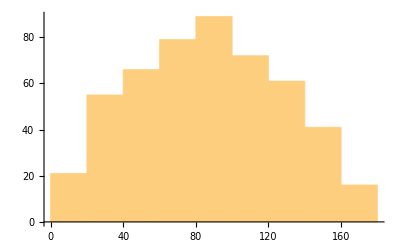

```mathematica
Histogram[ThetaList3[[5]]]
```

```mathematica
k=0;particleNo2=Table[k=k+1,{i,2000},{j,500}];
```

```mathematica
SetDirectory["/home/waleed/FourTb/MC_TrajProton/Spectra_BackDetMain/"]
```

/home/waleed/FourTb/MC_TrajProton/Spectra_BackDetMain

```mathematica
ParallelTable[
Export["Spectra"<>PackageString<>ToString[i-1]<>".txt",Transpose[{SetPrecision[ThetaList3[[i]],10],SetPrecision[PhiList3[[i]],10],SetPrecision[EeList3[[i]],10],particleNo2[[i]]}],"Table"],
{i,2000}];
```

### takes 2726s for 5e7_2e3

### 2992s for 10e7_2e7, 2 cores

```mathematica
Directory[]
```

/home/dmoser/FerencSource+Spectra/Mma_Spectra_5e7_2e3

# DumpSaving

```mathematica
DumpSaveDir=SpectrumDir
```

~/FerencSource+Spectra/Mma_Spectra_1e8_2e3_Glueck93_thMax45

```mathematica
SetDirectory[DumpSaveDir]
```

/home/dmoser/FerencSource+Spectra/Mma_Spectra_1e8_2e3_Glueck93_thMax45

```mathematica
DumpSave["EeList.mx",EeList];
```

```mathematica
DumpSave["TpList.mx",TpList];
```

```mathematica
DumpSave["ThetaList.mx",ThetaList];
```

```mathematica
DumpSave["PhiList.mx",PhiList];
```

# Dump loading

### we can also load from dump save

```mathematica
DumpLoadDir="~/FourTb/danielpc_MC/FerencSource+Spectra/Mma_Spectra_5e7_1e4";
```

```mathematica
SetDirectory[DumpLoadDir]
```

/home/waleed/FourTb/danielpc_MC/FerencSource+Spectra/Mma_Spectra_5e7_1e4

```mathematica
ClearAll[EeList]
```

```mathematica
Get["EeList.mx"]
```

```mathematica
EeList//Dimensions
```

{5000,10000}

```mathematica
EeList=Map[Partition[#,PackageSize]&,EeList];
```

```mathematica
EeList//Dimensions
```

{5000,5,2000}

```mathematica
EeList=Flatten[EeList,1];
```

```mathematica
EeList//Dimensions
```

{25000,2000}

### we can also load from dump save

```mathematica
ClearAll[EeList]
```

```mathematica
Get["TpList.mx"]
```

```mathematica
TpList//Dimensions
```

{5000,10000}

```mathematica
TpList=Map[Partition[#,PackageSize]&,TpList];
```

```mathematica
TpList//Dimensions
```

{5000,5,2000}

```mathematica
TpList=Flatten[TpList,1];
```

```mathematica
TpList//Dimensions
```

{25000,2000}

### we can also load from dump save

```mathematica
ClearAll[ThetaList]
```

```mathematica
Get["ThetaList.mx"]
```

```mathematica
ThetaList//Dimensions
```

{25000,2000}

```mathematica
ThetaList=Map[Partition[#,PackageSize]&,ThetaList];
```

```mathematica
ThetaList//Dimensions
```

{5000,5,2000}

```mathematica
ThetaList=Flatten[ThetaList,1];
```

```mathematica
ThetaList//Dimensions
```

{25000,2000}

### we can also load from dump save

```mathematica
ClearAll[EeList]
```

```mathematica
Get["PhiList.mx"]
```

```mathematica
PhiList//Dimensions
```

{5000,10000}

```mathematica
PhiList=Map[Partition[#,PackageSize]&,PhiList];
```

```mathematica
PhiList//Dimensions
```

{5000,5,2000}

```mathematica
PhiList=Flatten[PhiList,1];
```

```mathematica
PhiList//Dimensions
```

{25000,2000}

```mathematica
constList={{60,0.020001450687257744,0.0029287102319553357,0.06266117201211599},{120,0.017702432542715828,0.00242496244340481,0.06467212880684421},{180,0.017138760601011528,0.0019937951269802406,0.06702514608896595},{240,0.015879680596226953,0.001995550486038434,0.0668205199998191},{300,0.015315255566888527,0.0016826590536558781,0.06875544684765725},{360,0.015069073009898869,0.0014309957155937392,0.07072354535285344},{420,0.014715640521859193,0.0014186051346250037,0.07064213365873828},{480,0.013611942202238474,0.0013344743978295514,0.07132419992708464},{540,0.01350270760948456,0.0012366725298245283,0.07222764933101768},{600,0.013594431402549529,0.0010296669309730446,0.07434237623631264},{660,0.012747205553177054,0.001070582272322273,0.0736785884348348},{720,0.012084855286917174,0.0010087821442006162,0.07437739220552556},{780,0.011925699853453483,0.0009043688501574871,0.07558784806793274}};
```

```mathematica
c1=Interpolation[Transpose[{constList[[All,1]],constList[[All,2]]}]];c2=Interpolation[Transpose[{constList[[All,1]],constList[[All,3]]}]];c3=Interpolation[Transpose[{constList[[All,1]],constList[[All,4]]}]]ElectronSpectrumPDF=ProbabilityDistribution[weNormed[λ0,κ0,0,Ee],{Ee,me,E0}]
```

InterpolatingFunction[…]

```mathematica
c1Int=With[{},Compile[{{x,_Real}},Evaluate[N[c1[x]]],CompilationTarget->"C","RuntimeOptions"->"Speed",RuntimeAttributes->{Listable},CompilationOptions->{"InlineExternalDefinitions"->True}]];
c2Int=With[{},Compile[{{x,_Real}},Evaluate[N[c2[x]]],CompilationTarget->"C","RuntimeOptions"->"Speed",RuntimeAttributes->{Listable},CompilationOptions->{"InlineExternalDefinitions"->True}]];
c3Int=With[{},Compile[{{x,_Real}},Evaluate[N[c3[x]]],CompilationTarget->"C","RuntimeOptions"->"Speed",RuntimeAttributes->{Listable},CompilationOptions->{"InlineExternalDefinitions"->True}]];
```

```mathematica
func[en_,th_]:=c1Int[en]+c2Int[en]*E^(c3Int[en]*th)
```

```mathematica
func2[en_,th_]:=c1[en]+c2[en]*E^(c3[en]*th)
```

```mathematica
TofEe[Ee_]:=Ee-me;
```

```mathematica
normVal2=NIntegrate[weNormed[λ0,κ0,0,Ee]*Sin[th/180.*Pi]*func2[TofEe[Ee]/1000,th],{Ee,me,1.29258*^6},{th,0,90}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

12.2561

```mathematica
normedSPecAngInter=Interpolation[Table[{th,NIntegrate[weNormed[λ0,κ0,0,Ee]*Sin[th/180.*Pi]*func2[TofEe[Ee]/1000,th],{Ee,me,E0}]/normVal2},{th,0,90}]]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

InterpolatingFunction[…]

```mathematica
normedSPecInter=Interpolation[Table[{Ee,NIntegrate[weNormed[λ0,κ0,0,Ee]*Sin[th/180.*Pi]*func2[TofEe[Ee]/1000,th],{th,0,90}]/normVal2},{Ee,me,E0}]]
```

InterpolatingFunction::dmval: Input value {0.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

InterpolatingFunction[…]

```mathematica
Directory[]
```

/home/waleed/FourTb/MC_TrajProton/SpectraElec

```mathematica
Export["~/FourTb/MC_TrajProton/interSpec.mx",normedSPecInter]
```

~/FourTb/MC_TrajProton/interSpec.mx

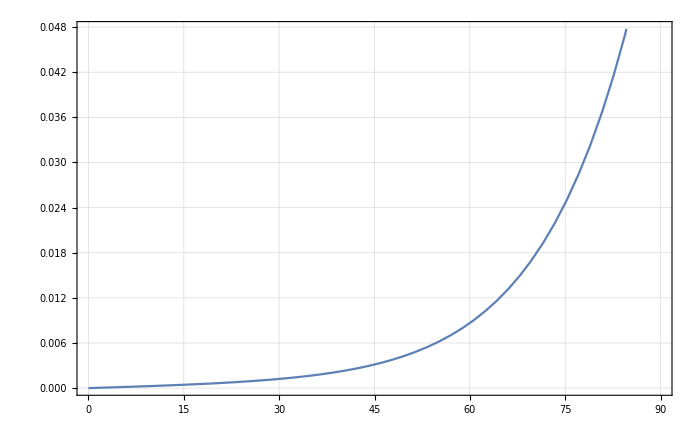

```mathematica
Plot[normedSPecAngInter[th],{th,0,90}]
```

```mathematica
probDistAttemptAng=ProbabilityDistribution[normedSPecAngInter[th],{th,0,90},Method->"Normalize"]
```

ProbabilityDistribution[1. InterpolatingFunction[…][x],{x,0,90}]

```mathematica
probDistAttempt=ProbabilityDistribution[normedSPecInter[Ee],{Ee,me,E0},Method->"Normalize"]
```

ProbabilityDistribution[1. InterpolatingFunction[…][x],{x,510999.,1.29258×10^6}]

```mathematica
RandomVariate[probDistAttempt,1]
```

{579707.}

```mathematica
t0=AbsoluteTime[];
thList2=ParallelTable[RandomVariate[probDistAttemptAng,PackageSize],{DataSets}];
t1=AbsoluteTime[];
t1-t0
```

43.812688

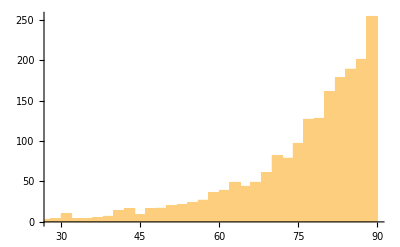

```mathematica
Histogram[thList2[[6]]]
```

```mathematica
t0=AbsoluteTime[];
EeList2=ParallelTable[RandomVariate[probDistAttempt,PackageSize]-me,{DataSets}];
t1=AbsoluteTime[];
t1-t0
```

1105.70656

```mathematica
enTabEl=Table[i,{i,60,780,60}];angTabEl={0,20,40,60,80};
```

```mathematica
Export["~/FourTb/MC_TrajProton/probDistAttempt.mx",normedSPecInter]
```

~/FourTb/MC_TrajProton/probDistAttempt.mx

```mathematica
PmmaAngDist=Table[Import["~/FourTb/Casino/Electron/"<>ToString[angTabEl[[ang]]]<>"deg/"<>ToString[enTabEl[[en]]]<>"BA.dat","Table",HeaderLines->2],{ang,Length[angTabEl]},{en,Length[enTabEl]}];
```

```mathematica
PmmaEnDist=Table[Import["~/FourTb/Casino/Electron/"<>ToString[angTabEl[[ang]]]<>"deg/"<>ToString[enTabEl[[en]]]<>"BE.dat","Table",HeaderLines->2],{ang,Length[angTabEl]},{en,Length[enTabEl]}];
```

```mathematica
rebinnedEnDist=Table[Table[{Sum[#[[j,1]],{j,i,i+9}]/10,Sum[#[[j,2]],{j,i,i+9}]/Total[#[[All,2]]]},{i,1,Length[#]-9,10}]&@PmmaEnDist[[ang,en]],{ang,Length[angTabEl]},{en,Length[enTabEl]}]
```

{1}
 |  |  |  |

```mathematica
rebinnedEnDistTest2=Flatten[Table[{{angTabEl[[ang]],enTabEl[[en]]},Table[{Sum[#[[j,1]],{j,i,i+9}]/10,Sum[#[[j,2]],{j,i,i+9}]/Total[#[[All,2]]]},{i,1,Length[#]-9,10}]&@PmmaEnDist[[ang,en]]},{ang,Length[angTabEl]},{en,Length[enTabEl]}],1]
```

{{{0,60},{{0.541082,0.},{1.74349,0.00119047},{2.94589,0.00317461},{4.1483,0.00357143},{5.3507,0.00515874},{6.55311,0.00674604},{7.75551,0.00753968},{8.95792,0.00595238},{10.1603,0.00833335},32,{49.8397,0.022619},{51.0421,0.0222222},{52.2445,0.0146826},{53.4469,0.0246032},{54.6493,0.0178571},{55.8517,0.0186508},{57.0541,0.0178571},{58.2565,0.0226191},{59.4589,0.015873}}},63,{{80,780},{1}}}
 |  |  |  |

```mathematica
rebinnedAngDist=Table[Table[{Sum[#[[j,1]],{j,i,i+4}]/5,Sum[#[[j,2]],{j,i,i+4}]/Total[#[[All,2]]]},{i,1,Length[#]-4,5}]&@PmmaAngDist[[ang,en]],{ang,Length[angTabEl]},{en,Length[enTabEl]}];
```

```mathematica
rebinnedAngDistTest=Flatten[Table[{{angTabEl[[ang]],enTabEl[[en]]},Table[{Sum[#[[j,1]],{j,i,i+4}]/5,Sum[#[[j,2]],{j,i,i+4}]/Total[#[[All,2]]]},{i,1,Length[#]-4,5}]&@PmmaAngDist[[ang,en]]},{ang,Length[angTabEl]},{en,Length[enTabEl]}],1];
```

```mathematica
rebinnedAngDistTest//Dimensions
```

{65,2}

```mathematica
enTabEl//Length
```

13

```mathematica
rebinnedAngDistTest[[1,1]]
```

{0,60}

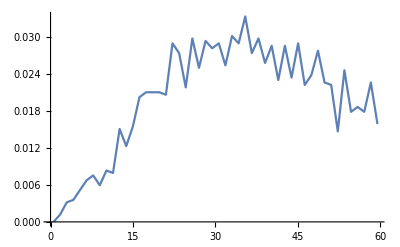

```mathematica
ListLinePlot[rebinnedEnDist[[1,1]]]
```

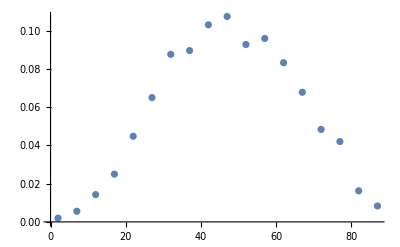

```mathematica
ListPlot[rebinnedAngDist[[1,1]]]
```

```mathematica
interTableEnDistTest=Interpolation[rebinnedEnDistTest2,InterpolationOrder->1]
```

InterpolatingFunction[…]

```mathematica
interTableAngDistTest=Interpolation[rebinnedAngDistTest,InterpolationOrder->1]
```

InterpolatingFunction[…]

```mathematica
interTableEnDistTest2=With[{},Compile[{{ang,_Real},{en,_Real}},Evaluate[N[interTableEnDistTest[ang,en]]],CompilationTarget->"C","RuntimeOptions"->"Speed",RuntimeAttributes->{Listable},CompilationOptions->{"InlineExternalDefinitions"->True}]]
```

CompiledFunction[…]

```mathematica
t0=AbsoluteTime[];ThetaList3=Quiet[ParallelTable[RandomVariate[ProbabilityDistribution[Interpolation[interTableAngDistTest[thList2[[j,i]],EeList2[[j,i]]/1000]][th],{th,0,90},Method->"Normalize"]],{j,500},{i,2000}]];t1=AbsoluteTime[];
t1-t0
```

InterpolatingFunction::dmval: Input value {89.1891,384.687} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {88.6427,536.276} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {84.7377,439.71} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {82.6903,460.084} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.04801} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {88.6494} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {88.8561} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

General::stop: Further output of ProbabilityDistribution::nvpdf will be suppressed during this calculation.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

General::stop: Further output of ProbabilityDistribution::nvpdf will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {80.9016,248.492} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.04801} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {88.6494} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

General::stop: Further output of ProbabilityDistribution::nvpdf will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.04801} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {88.6494} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {88.8561} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

General::stop: Further output of ProbabilityDistribution::nvpdf will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {84.5801,516.892} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.04801} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {88.6494} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

General::stop: Further output of ProbabilityDistribution::nvpdf will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {89.7746,168.44} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.04801} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {88.6494} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

InterpolatingFunction::dmval: Input value {82.9394,340.526} lies outside the range of data in the interpolating function. Extrapolation will be used.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

InterpolatingFunction::dmval: Input value {1.04801} lies outside the range of data in the interpolating function. Extrapolation will be used.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

InterpolatingFunction::dmval: Input value {88.6494} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of ProbabilityDistribution::nvpdf will be suppressed during this calculation.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

General::stop: Further output of ProbabilityDistribution::nvpdf will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.04801} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {88.6494} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {88.8561} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

General::stop: Further output of ProbabilityDistribution::nvpdf will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.04801} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {88.6494} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {88.8561} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

General::stop: Further output of ProbabilityDistribution::nvpdf will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.04801} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {88.6494} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {88.8561} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

General::stop: Further output of ProbabilityDistribution::nvpdf will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.04801} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {88.6494} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {88.8561} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

General::stop: Further output of ProbabilityDistribution::nvpdf will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {83.8766,301.474} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.04801} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {88.6494} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.04801} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {88.6494} lies outside the range of data in the interpolating function. Extrapolation will be used.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

InterpolatingFunction::dmval: Input value {88.8561} lies outside the range of data in the interpolating function. Extrapolation will be used.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

General::stop: Further output of ProbabilityDistribution::nvpdf will be suppressed during this calculation.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

General::stop: Further output of ProbabilityDistribution::nvpdf will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {88.5222,107.453} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.04801} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {88.6494} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

General::stop: Further output of ProbabilityDistribution::nvpdf will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {84.9497,318.122} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.04801} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {88.6494} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.04801} lies outside the range of data in the interpolating function. Extrapolation will be used.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

InterpolatingFunction::dmval: Input value {88.6494} lies outside the range of data in the interpolating function. Extrapolation will be used.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

InterpolatingFunction::dmval: Input value {88.8561} lies outside the range of data in the interpolating function. Extrapolation will be used.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

General::stop: Further output of ProbabilityDistribution::nvpdf will be suppressed during this calculation.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

General::stop: Further output of ProbabilityDistribution::nvpdf will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {87.4758,289.176} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.04801} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {88.6494} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

InterpolatingFunction::dmval: Input value {81.1312,503.705} lies outside the range of data in the interpolating function. Extrapolation will be used.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

InterpolatingFunction::dmval: Input value {1.04801} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of ProbabilityDistribution::nvpdf will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {88.6494} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

General::stop: Further output of ProbabilityDistribution::nvpdf will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.04801} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {88.6494} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {88.8561} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

General::stop: Further output of ProbabilityDistribution::nvpdf will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {87.7115,452.042} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.04801} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {88.6494} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

General::stop: Further output of ProbabilityDistribution::nvpdf will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {85.616,140.234} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.04801} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {88.6494} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

General::stop: Further output of ProbabilityDistribution::nvpdf will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {87.7492,56.7609} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.04801} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {88.6494} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

General::stop: Further output of ProbabilityDistribution::nvpdf will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {74.5497,18.2834} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.04801} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {88.6494} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

General::stop: Further output of ProbabilityDistribution::nvpdf will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.04801} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {88.6494} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {88.8561} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

General::stop: Further output of ProbabilityDistribution::nvpdf will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.04801} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {88.6494} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {88.8561} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

General::stop: Further output of ProbabilityDistribution::nvpdf will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {60.4404,47.5805} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.04801} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {88.6494} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

General::stop: Further output of ProbabilityDistribution::nvpdf will be suppressed during this calculation.

4570.250693

```mathematica
t0=AbsoluteTime[];ThetaList4=Quiet[ParallelTable[RandomVariate[ProbabilityDistribution[Interpolation[interTableAngDistTest[thList2[[j,i]],EeList2[[j,i]]/1000]][th],{th,0,90},Method->"Normalize"]],{j,500,1000},{i,2000}]];t1=AbsoluteTime[];
t1-t0
```

InterpolatingFunction::dmval: Input value {1.04801} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {83.8366,502.191} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {89.7326,326.492} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {88.6494} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.04801} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {88.8561} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {88.6494} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

General::stop: Further output of ProbabilityDistribution::nvpdf will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {80.6452,131.8} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.04801} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {88.6494} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

General::stop: Further output of ProbabilityDistribution::nvpdf will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {87.1443,84.472} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.04801} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {88.6494} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

General::stop: Further output of ProbabilityDistribution::nvpdf will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.04801} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {88.6494} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {88.8561} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

General::stop: Further output of ProbabilityDistribution::nvpdf will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.04801} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {88.6494} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {88.8561} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

General::stop: Further output of ProbabilityDistribution::nvpdf will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.04801} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {88.6494} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {88.8561} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

General::stop: Further output of ProbabilityDistribution::nvpdf will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {87.9706,493.527} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.04801} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {88.6494} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

General::stop: Further output of ProbabilityDistribution::nvpdf will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.04801} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {88.6494} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {88.8561} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

General::stop: Further output of ProbabilityDistribution::nvpdf will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {83.3827,567.957} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.04801} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {88.6494} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

General::stop: Further output of ProbabilityDistribution::nvpdf will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.04801} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {88.6494} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {88.8561} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

General::stop: Further output of ProbabilityDistribution::nvpdf will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {81.2725,462.35} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.04801} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {88.6494} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

General::stop: Further output of ProbabilityDistribution::nvpdf will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {79.5604,42.7552} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.04801} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {88.6494} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

General::stop: Further output of ProbabilityDistribution::nvpdf will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.04801} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {88.6494} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {88.8561} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

General::stop: Further output of ProbabilityDistribution::nvpdf will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {85.2755,219.91} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.04801} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {88.6494} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

General::stop: Further output of ProbabilityDistribution::nvpdf will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.04801} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {88.6494} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {88.8561} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

General::stop: Further output of ProbabilityDistribution::nvpdf will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.04801} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {88.6494} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {88.8561} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

General::stop: Further output of ProbabilityDistribution::nvpdf will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.04801} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {88.6494} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {88.8561} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

General::stop: Further output of ProbabilityDistribution::nvpdf will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {86.5655,538.815} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.04801} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {88.6494} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

General::stop: Further output of ProbabilityDistribution::nvpdf will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.04801} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {88.6494} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {88.8561} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

General::stop: Further output of ProbabilityDistribution::nvpdf will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {88.7394,160.259} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.04801} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {88.6494} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

General::stop: Further output of ProbabilityDistribution::nvpdf will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.04801} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {88.6494} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {88.8561} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

General::stop: Further output of ProbabilityDistribution::nvpdf will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {68.515,33.8386} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.04801} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {88.6494} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

General::stop: Further output of ProbabilityDistribution::nvpdf will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.04801} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {88.6494} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {88.8561} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

General::stop: Further output of ProbabilityDistribution::nvpdf will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {84.9668,287.114} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.04801} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {88.6494} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

General::stop: Further output of ProbabilityDistribution::nvpdf will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {88.7676,245.76} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.04801} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {88.6494} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

General::stop: Further output of ProbabilityDistribution::nvpdf will be suppressed during this calculation.

4564.342924

```mathematica
t0=AbsoluteTime[];EeList4=Quiet[ParallelTable[RandomVariate[ProbabilityDistribution[Interpolation[interTableEnDistTest[thList2[[j,i]],EeList2[[j,i]]/1000]][en],{en,0/1000,EeList2[[j,i]]/1000},Method->"Normalize"]],{j,500,1000},{i,2000}]];t1=AbsoluteTime[];
t1-t0
```

InterpolatingFunction::dmval: Input value {1.28582} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.76918} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.12709} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.93504} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {83.8366,502.191} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {89.7326,326.492} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {164.451} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {482.062} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {272.046} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {375.38} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.92611} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.5525} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.14382} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.35292} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.89218} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.61091} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {502.133} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {326.455} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

General::stop: Further output of ProbabilityDistribution::nvpdf will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {80.6452,131.8} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.0304} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {131.784} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

General::stop: Further output of ProbabilityDistribution::nvpdf will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {87.1443,84.472} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.660398} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {84.4622} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

General::stop: Further output of ProbabilityDistribution::nvpdf will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {4.17574} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {534.061} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.71459} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

General::stop: Further output of ProbabilityDistribution::nvpdf will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.1309} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {144.637} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.00601} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

General::stop: Further output of ProbabilityDistribution::nvpdf will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {2.44137} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {312.241} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.17176} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

General::stop: Further output of ProbabilityDistribution::nvpdf will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {87.9706,493.527} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.85837} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {493.47} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

General::stop: Further output of ProbabilityDistribution::nvpdf will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {5.65704} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {723.513} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {5.0323} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

General::stop: Further output of ProbabilityDistribution::nvpdf will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {83.3827,567.957} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.44026} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {567.891} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

General::stop: Further output of ProbabilityDistribution::nvpdf will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.02215} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {130.729} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.90927} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

General::stop: Further output of ProbabilityDistribution::nvpdf will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {81.2725,462.35} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.61463} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {462.297} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

General::stop: Further output of ProbabilityDistribution::nvpdf will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {79.5604,42.7552} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.334259} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {42.7503} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

General::stop: Further output of ProbabilityDistribution::nvpdf will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.891755} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {114.052} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.793274} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

General::stop: Further output of ProbabilityDistribution::nvpdf will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {85.2755,219.91} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.71925} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {219.885} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

General::stop: Further output of ProbabilityDistribution::nvpdf will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.74776} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {223.532} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.55475} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

InterpolatingFunction::dmval: Input value {3.6461} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of ProbabilityDistribution::nvpdf will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {466.322} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.24344} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

General::stop: Further output of ProbabilityDistribution::nvpdf will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.32927} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {170.009} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.18247} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

General::stop: Further output of ProbabilityDistribution::nvpdf will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {86.5655,538.815} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.21243} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {538.753} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.50983} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {448.893} lies outside the range of data in the interpolating function. Extrapolation will be used.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

InterpolatingFunction::dmval: Input value {3.12222} lies outside the range of data in the interpolating function. Extrapolation will be used.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

General::stop: Further output of ProbabilityDistribution::nvpdf will be suppressed during this calculation.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

General::stop: Further output of ProbabilityDistribution::nvpdf will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {88.7394,160.259} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.2529} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {160.241} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

General::stop: Further output of ProbabilityDistribution::nvpdf will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {2.85437} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {365.062} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.53914} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

General::stop: Further output of ProbabilityDistribution::nvpdf will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {68.515,33.8386} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.264548} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {33.8347} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

General::stop: Further output of ProbabilityDistribution::nvpdf will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.501544} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {64.1455} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.446156} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

General::stop: Further output of ProbabilityDistribution::nvpdf will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {84.9668,287.114} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.24464} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {287.081} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

General::stop: Further output of ProbabilityDistribution::nvpdf will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {88.7676,245.76} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.92134} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {245.732} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

General::stop: Further output of ProbabilityDistribution::nvpdf will be suppressed during this calculation.

8206.917767

```mathematica
t0=AbsoluteTime[];EeList3=Quiet[ParallelTable[RandomVariate[ProbabilityDistribution[Interpolation[interTableEnDistTest[thList2[[j,i]],EeList2[[j,i]]/1000]][en],{en,0/1000,EeList2[[j,i]]/1000},Method->"Normalize"]],{j,500},{i,2000}]];t1=AbsoluteTime[];
t1-t0
```

InterpolatingFunction::dmval: Input value {89.1891,384.687} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.953304} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {84.7377,439.71} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {82.6903,460.084} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.00747} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {121.924} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.793887} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {88.6427,536.276} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.43763} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.59692} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {384.643} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.848025} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {101.535} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.19258} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {439.659} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {460.031} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.706213} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {536.214} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

General::stop: Further output of ProbabilityDistribution::nvpdf will be suppressed during this calculation.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

General::stop: Further output of ProbabilityDistribution::nvpdf will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {80.9016,248.492} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.9427} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {248.463} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

General::stop: Further output of ProbabilityDistribution::nvpdf will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.10862} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {141.787} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.986184} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

General::stop: Further output of ProbabilityDistribution::nvpdf will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {84.5801,516.892} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.04104} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {516.832} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

General::stop: Further output of ProbabilityDistribution::nvpdf will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {89.7746,168.44} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.31686} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {168.421} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

General::stop: Further output of ProbabilityDistribution::nvpdf will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {82.9394,340.526} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.66222} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {340.487} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

InterpolatingFunction::dmval: Input value {1.95182} lies outside the range of data in the interpolating function. Extrapolation will be used.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

InterpolatingFunction::dmval: Input value {249.63} lies outside the range of data in the interpolating function. Extrapolation will be used.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

InterpolatingFunction::dmval: Input value {1.73627} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of ProbabilityDistribution::nvpdf will be suppressed during this calculation.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

General::stop: Further output of ProbabilityDistribution::nvpdf will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.621} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {207.319} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.44198} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

General::stop: Further output of ProbabilityDistribution::nvpdf will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.23518} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {157.975} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.09877} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

General::stop: Further output of ProbabilityDistribution::nvpdf will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {4.18032} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {534.646} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.71867} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

General::stop: Further output of ProbabilityDistribution::nvpdf will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {83.8766,301.474} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.35691} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {301.44} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

General::stop: Further output of ProbabilityDistribution::nvpdf will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.69565} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {216.867} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.50839} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

General::stop: Further output of ProbabilityDistribution::nvpdf will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {88.5222,107.453} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.84006} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {107.44} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

General::stop: Further output of ProbabilityDistribution::nvpdf will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {84.9497,318.122} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.48706} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {318.085} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

General::stop: Further output of ProbabilityDistribution::nvpdf will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {3.77039} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {482.217} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.354} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

General::stop: Further output of ProbabilityDistribution::nvpdf will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {87.4758,289.176} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.26077} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {289.143} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

General::stop: Further output of ProbabilityDistribution::nvpdf will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {81.1312,503.705} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.93794} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {503.646} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

General::stop: Further output of ProbabilityDistribution::nvpdf will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.63715} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {209.385} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.45635} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

General::stop: Further output of ProbabilityDistribution::nvpdf will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {87.7115,452.042} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.53404} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {451.99} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

General::stop: Further output of ProbabilityDistribution::nvpdf will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {85.616,140.234} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.09634} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {140.218} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

General::stop: Further output of ProbabilityDistribution::nvpdf will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {87.7492,56.7609} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.443755} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {56.7544} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

General::stop: Further output of ProbabilityDistribution::nvpdf will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {74.5497,18.2834} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.142938} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {18.2812} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

General::stop: Further output of ProbabilityDistribution::nvpdf will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {3.66046} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {468.158} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.25622} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

General::stop: Further output of ProbabilityDistribution::nvpdf will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {4.09241} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {523.403} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.64046} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

General::stop: Further output of ProbabilityDistribution::nvpdf will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {60.4404,47.5805} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.371982} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {47.575} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

ProbabilityDistribution::nvpdf: The PDF of the given distribution is not non-negative.

General::stop: Further output of ProbabilityDistribution::nvpdf will be suppressed during this calculation.

8194.7206

```mathematica
Export["/home/waleed/FourTb/MC_TrajProton/ThetaList3.m",ThetaList3]
```

/home/waleed/FourTb/MC_TrajProton/ThetaList3.m

```mathematica
DataSets
```

5000

```mathematica
SetDirectory["/home/waleed/FourTb/MC_TrajProton/BSStudy"]
```

/home/waleed/FourTb/MC_TrajProton/BSStudy

```mathematica
ParallelTable[
Export["Spectra"<>PackageString<>ToString[i-1+500]<>".txt",Transpose[{SetPrecision[ThetaList4[[i]],10],SetPrecision[PhiList[[i]],10],SetPrecision[EeList4[[i]],10],SetPrecision[TpList[[i]],10]}],"Table"],
{i,500}];
```

```mathematica
ParallelTable[
Export["Spectra"<>PackageString<>ToString[i-1]<>".txt",Transpose[{SetPrecision[ThetaList3[[i]],10],SetPrecision[PhiList[[i]],10],SetPrecision[EeList3[[i]],10],SetPrecision[TpList[[i]],10]}],"Table"],
{i,500}];
```

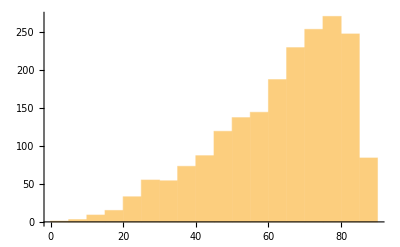

```mathematica
Histogram[ThetaList3[[1]]]
```

```mathematica
probDistAttemptBS
```

InterpolatingFunction::dmval: Input value {90,720} lies outside the range of data in the interpolating function. Extrapolation will be used.

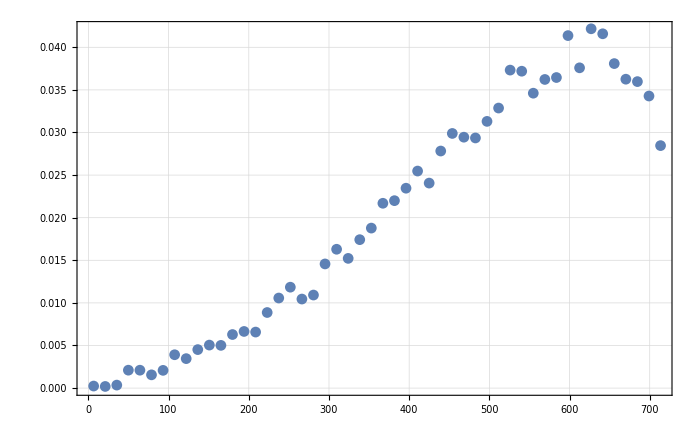

```mathematica
ListPlot[interTableEnDistTest[90,720]]
```

```mathematica
normTableEnDistTest=With[{leftAng=interTableEnDistTest["Domain"][[1,1]],rightAng=interTableEnDistTest["Domain"][[1,2]],leftEn=interTableEnDistTest["Domain"][[2,1]],rightEn=interTableEnDistTest["Domain"][[2,2]]},NIntegrate[If[leftAng≤bAng≤rightAng&& leftEn≤bAng≤rightEn,interTableEnDistTest[bsen,bsang],0],{bAng,0,enTabEl[[En]]}]],{thIn,Length[angTabEl]}
```

```mathematica
interTableEnDist=Table[Interpolation[rebinnedEnDist[[ang,En]],"ExtrapolationHandler"->{0 &, "WarningMessage"->False}],{ang,Length[angTabEl]},{En,1,Length[enTabEl]}] ;
```

```mathematica
interTableAngDist=Table[Interpolation[rebinnedAngDist[[ang,En]],"ExtrapolationHandler"->{0 &, "WarningMessage"->False}],{ang,Length[angTabEl]},{En,1,Length[enTabEl]}] ;
```

```mathematica
normTableEnDist=Table[With[{left=interTableEnDist[[thIn,En]]["Domain"][[1,1]],right=interTableEnDist[[thIn,En]]["Domain"][[1,2]]},NIntegrate[If[left≤bsen≤right,interTableEnDist[[thIn,En]][bsen],0],{bsen,0,enTabEl[[En]]}]],{thIn,Length[angTabEl]},{En,1,Length[enTabEl]}]
```

{{1.19493,2.3811,3.58411,4.77851,5.96038,7.16705,8.35371,9.55053,10.7635,11.9522,13.2086,14.3089,15.515},{1.19333,2.38826,3.58785,4.77272,5.93741,7.17153,8.29403,9.50453,10.7373,11.9482,13.1008,14.3933,15.5447},{1.19187,2.38542,3.5854,4.76738,5.9604,7.18075,8.34406,9.54885,10.7477,11.9583,13.1477,14.3253,15.5566},{1.19635,2.39064,3.58607,4.78475,5.98201,7.17367,8.3705,9.56143,10.7625,11.9683,13.1517,14.3564,15.5651},{1.18112,2.36473,3.54875,4.73525,5.92415,7.11472,8.3027,9.48371,10.6927,11.8702,13.0893,14.2745,15.4581}}

```mathematica
normTableAngDist=Table[With[{left=interTableAngDist[[thIn,En]]["Domain"][[1,1]],right=interTableAngDist[[thIn,En]]["Domain"][[1,2]]},NIntegrate[If[left≤bsen≤right,interTableAngDist[[thIn,En]][bsen],0],{bsen,1,enTabEl[[En+1]]}]],{thIn,Length[angTabEl]},{En,1,Length[enTabEl]-1}]
```

{{4.96577,4.97373,4.97442,4.99379,4.99198,4.98813,4.99103,4.98884,4.99015,4.99491,4.9872,4.98953},{5.0014,4.98707,4.99266,4.98932,4.97043,4.99618,4.9985,4.97558,4.98509,4.99592,4.98958,5.00147},{4.98463,5.0004,4.99309,4.98856,4.98731,4.9843,4.98853,4.99249,4.98703,4.9949,4.98035,4.98206},{4.98279,4.98123,4.98461,4.98576,4.98148,4.98423,4.98381,4.98671,4.97619,4.97701,4.98607,4.98591},{4.89786,4.88687,4.88637,4.89037,4.88718,4.88389,4.88167,4.88227,4.89069,4.88305,4.88957,4.89115}}

```mathematica
E0-me
```

781582.

```mathematica
781581.8581615719+me
```

1.29258×10^6

```mathematica
angTabEl
```

{0,20,40,60,80}

```mathematica
normTableEnDist[[ang,en]]
```

```mathematica
enTabEl
```

{60,120,180,240,300,360,420,480,540,600,660,720,780}

```mathematica
normValWeNormed=NIntegrate[weNormed[λ0,κ0,0,Ee],{Ee,me,E0}]
```

1.

```mathematica
normValAngSpec=NIntegrate[Sin[th/180.*Pi],{th,0,90}]
```

57.2958

```mathematica
probTableElecSpec//Length
```

12

```mathematica
enTabEl//Length
```

13

```mathematica
enTabEl[[3]]*1000+me
```

690999.

```mathematica
enTabEl[[3+1]]*1000+me
```

750999.

```mathematica
E0
```

1.29258×10^6

```mathematica
NIntegrate[weNormed[λ0,κ0,0,Ee],{Ee,enTabEl[[3]]*1000+me,enTabEl[[3+1]]*1000+me}]
```

0.126209

```mathematica
Plot[weNormed[λ0,κ0,0,Ee],{Ee,me,E0}]
```

-Graphics-

```mathematica
probTableElecSpec=Table[Which[i==1,NIntegrate[weNormed[λ0,κ0,0,Ee],{Ee,me,enTabEl[[1]]*1000+me}],
i==Length[enTabEl]-1,NIntegrate[weNormed[λ0,κ0,0,Ee],{Ee,enTabEl[[i]]*1000+me,E0}],
True,NIntegrate[weNormed[λ0,κ0,0,Ee],{Ee,enTabEl[[i]]*1000+me,enTabEl[[i+1]]*1000+me}]],{i,Length[enTabEl]-1}]
```

{0.0561914,0.116788,0.126209,0.126915,0.120247,0.107486,0.0900706,0.0696785,0.0482657,0.0280825,0.0116803,0.00190969}

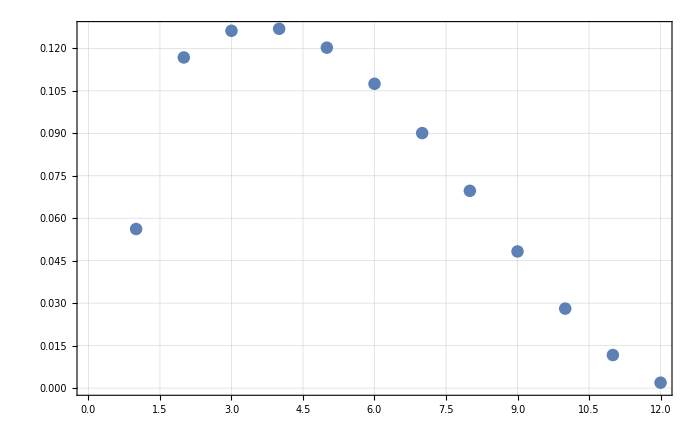

```mathematica
ListPlot[probTableElecSpec]
```

```mathematica
probTableElecSpecAng=Table[Which[i==Length[angTabEl],NIntegrate[Sin[th/180.*Pi]/normValAngSpec,{th,angTabEl[[i]],90}],
True,NIntegrate[Sin[th/180.*Pi]/normValAngSpec,{th,angTabEl[[i]],angTabEl[[i+1]]}]],{i,Length[angTabEl]}]
```

{0.0603074,0.173648,0.266044,0.326352,0.173648}

```mathematica
interTableEnDist[[1,1]]*interTableAngDist[[1,1]]
```

InterpolatingFunction[…] InterpolatingFunction[…]

```mathematica
normTableEnDist//Dimensions
```

{5,13}

```mathematica
probDistTable=Table[ProbabilityDistribution[(interTableEnDist[[ang,en]]/normTableEnDist[[ang,en]])[Ee],{Ee,0,enTabEl[[en]]},Method->"Normalize"],{ang,Length[angTabEl]},{en,Length[enTabEl]}];
```

```mathematica
RandomVariate[probDistEnDist]
```

31.2918

```mathematica
enTab=Table[probTableElecSpec[[i]]*probTableElecSpecAng[[i]]*func2[TofEe[Ee]/1000,th]*interTableEnDist[[ang,en]]/normTableEnDist[[ang,en]]*interTableAngDist[[ang,en]]/normTableAngDist[[ang,en]]
```

```mathematica
Table[{Ee,NIntegrate[weNormed[λ0,κ0,0,Ee]*Sin[th/180.*Pi]*func2[TofEe[Ee]/1000,th],{th,0,90}]/normVal2},{Ee,me,E0}]]
```

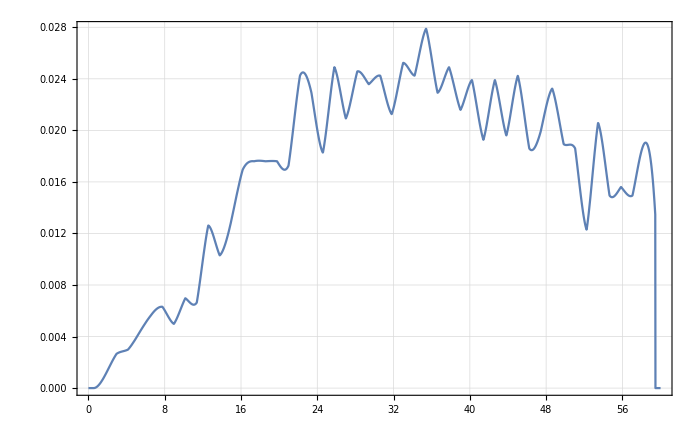

```mathematica
Plot[interTableEnDist[[1,1]][x]/normTableEnDist[[1,1]],{x,0,60}]
```

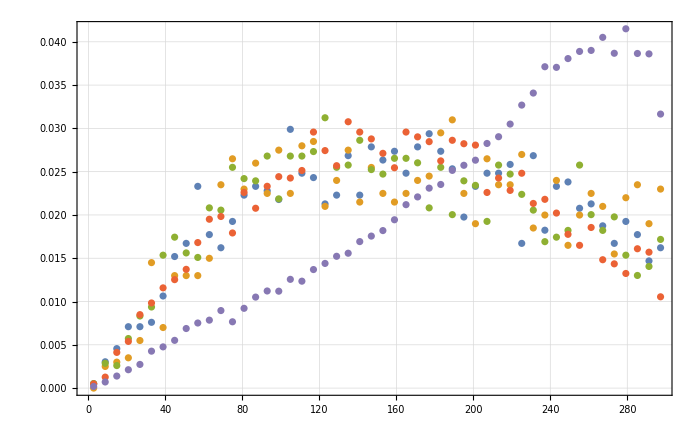

```mathematica
Show[ListPlot[rebinnedEnDist[[All,5]]]]
```

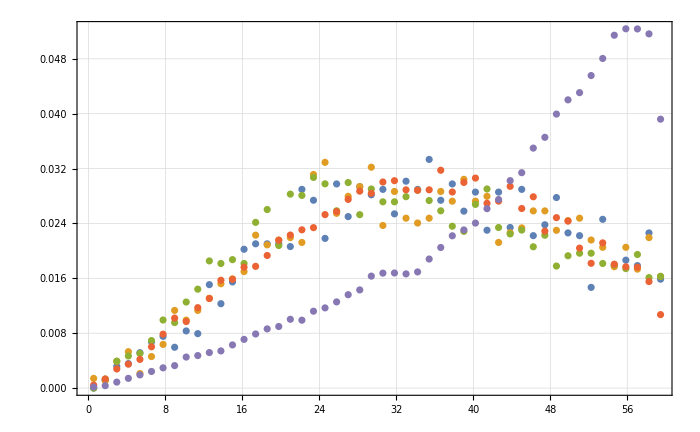

```mathematica
Show[ListPlot[rebinnedEnDist[[All,1]]]]
```

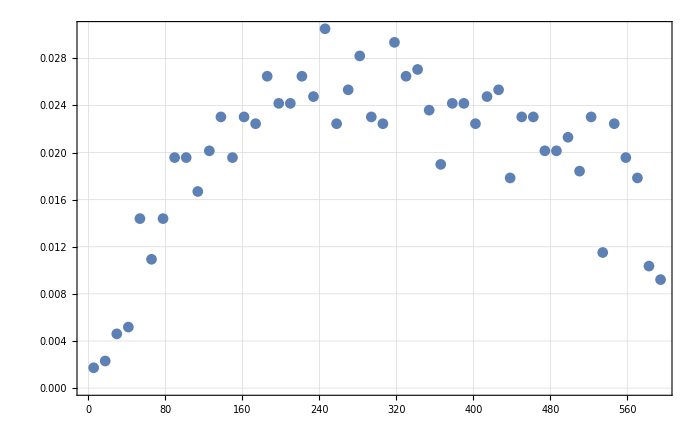

```mathematica
ListPlot[rebinnedEnDist[[2,10]]]
```

```mathematica
testJInter=Interpolation[rebinnedEnDist2]
```

Interpolation::indat: Data point {{{60,0},{{0.541082,0.},{1.74349,0.00119047},{2.94589,0.00317461},{4.1483,0.00357143},{5.3507,0.00515874},{6.55311,0.00674604},{7.75551,0.00753968},{8.95792,0.00595238},{10.1603,0.00833335},{11.3627,0.00793651},«31»,{49.8397,0.022619},{51.0421,0.0222222},{52.2445,0.0146826},{53.4469,0.0246032},{54.6493,0.0178571},{55.8517,0.0186508},{57.0541,0.0178571},{58.2565,0.0226191},{59.4589,0.015873}}},«11»,{{780,0},{{«1»},«48»,«1»}}} contains abscissa {{60,0},{{0.541082,0.},{1.74349,0.00119047},{2.94589,0.00317461},{4.1483,0.00357143},{5.3507,0.00515874},{6.55311,0.00674604},{7.75551,0.00753968},{8.95792,0.00595238},{10.1603,0.00833335},{11.3627,0.00793651},«31»,{49.8397,0.022619},{51.0421,0.0222222},{52.2445,0.0146826},{53.4469,0.0246032},{54.6493,0.0178571},{55.8517,0.0186508},{57.0541,0.0178571},{58.2565,0.0226191},{59.4589,0.015873}}}, which is not a real number.

Interpolation[{1}]
 |  |  |  |

```mathematica
testJInter[1,0]
```

Interpolation[{{1},3,{{{60,80},{{0.541082,0.000152959},{1.74349,0.00034962},{2.94589,0.000874049},{4.1483,0.00142033},{5.3507,0.00192291},{6.55311,0.00242549},{7.75551,0.00294992},{8.95792,0.00327769},{10.1603,0.00452321},{11.3627,0.00474172},{12.5651,0.00517874},{13.7675,0.00541911},{14.9699,0.00629316},{16.1723,0.00710166},{17.3748,0.0078883},{18.5772,0.00863124},{19.7796,0.00898087},{20.982,0.0100297},14,{39.018,0.0230531},{40.2204,0.0240582},{41.4228,0.0261559},{42.6253,0.0274889},{43.8277,0.0302421},{45.0301,0.0314002},{46.2325,0.0349839},{47.4349,0.0365571},{48.6373,0.0399441},{49.8397,0.0420199},{51.0421,0.0430688},{52.2445,0.0455598},{53.4469,0.0480509},{54.6493,0.0514378},{55.8517,0.0523774},{57.0541,0.0523556},{58.2565,0.0516345},{59.4589,0.0392011}}},11,{{780,80},{1}}}}][1,0]
 |  |  |  |

```mathematica
rebinnedEnDist2[[1,1]]
```

{60,0,{{0.541082,0.},{1.74349,0.00119047},{2.94589,0.00317461},{4.1483,0.00357143},{5.3507,0.00515874},{6.55311,0.00674604},{7.75551,0.00753968},{8.95792,0.00595238},{10.1603,0.00833335},{11.3627,0.00793651},{12.5651,0.0150794},{13.7675,0.0123016},{14.9699,0.0154762},{16.1723,0.0202381},{17.3748,0.0210317},{18.5772,0.0210317},{19.7796,0.0210317},{20.982,0.0206349},{22.1844,0.0289683},{23.3868,0.0273809},{24.5892,0.0218254},{25.7916,0.0297619},{26.994,0.025},{28.1964,0.0293651},{29.3988,0.0281746},{30.6012,0.0289682},{31.8036,0.0253968},{33.006,0.0301587},{34.2084,0.0289683},{35.4108,0.0333333},{36.6132,0.0273809},{37.8156,0.0297619},{39.018,0.0257936},{40.2204,0.0285714},{41.4228,0.0230159},{42.6253,0.0285714},{43.8277,0.0234127},{45.0301,0.0289683},{46.2325,0.0222222},{47.4349,0.0238095},{48.6373,0.0277778},{49.8397,0.022619},{51.0421,0.0222222},{52.2445,0.0146826},{53.4469,0.0246032},{54.6493,0.0178571},{55.8517,0.0186508},{57.0541,0.0178571},{58.2565,0.0226191},{59.4589,0.015873}}}

```mathematica
500/20
```

25

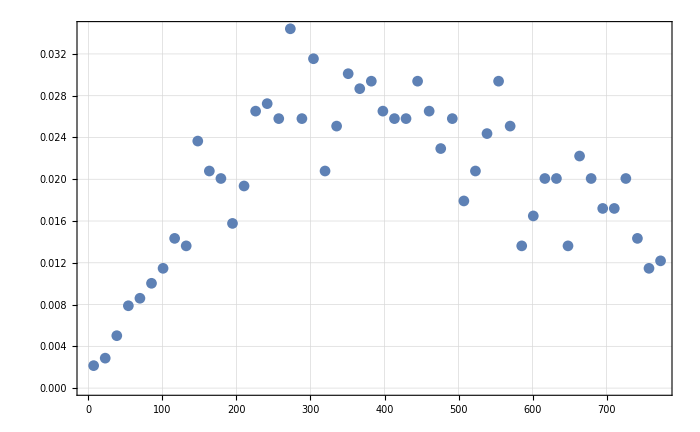

3

```mathematica
ListPlot[rebinnedEnDist[[1,13]]]
```

```mathematica
Length[enTabEl]
```

13